```mathematica
X1=Table[Con1[[i]],{i,1,13}];
X2=Table[Con2[[i]],{i,1,30}];
```

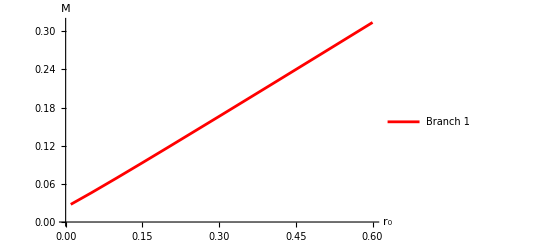

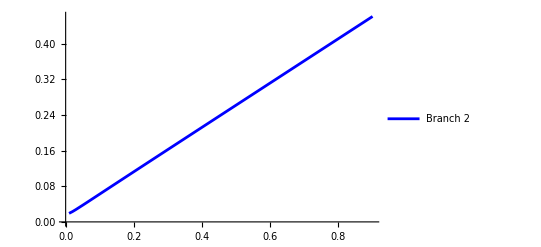

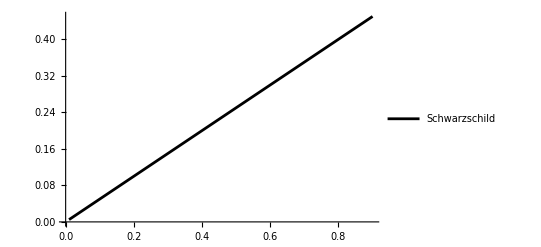

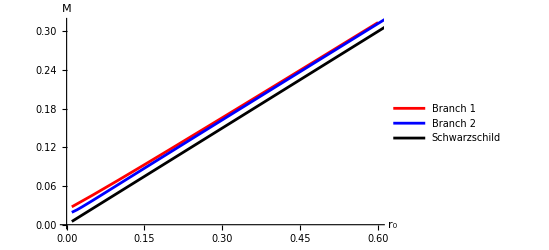

```mathematica
ListPlot[Table[{X1[[i]][[1]],X1[[i]][[3]]},{i,1,10}], Joined->True,PlotStyle->Red,AxesLabel->{Style[" r_0",FontSize->20],Style["M", FontSize->20]},PlotLegends->Placed[{"Branch 1"},{0.2,0.9}]]
ListPlot[Table[{X2[[i]][[1]],X2[[i]][[3]]},{i,1,30}],Joined->True,PlotStyle->Blue,PlotLegends->Placed[{"Branch 2"},{0.2,0.8}]]
ListPlot[Table[{X2[[i]][[1]],X2[[i]][[1]]/2},{i,1,30}],Joined->True,PlotStyle->Black,PlotLegends->Placed[{"Schwarzschild"},{0.24,0.7}]]
Show[%%%,%%,%]
```

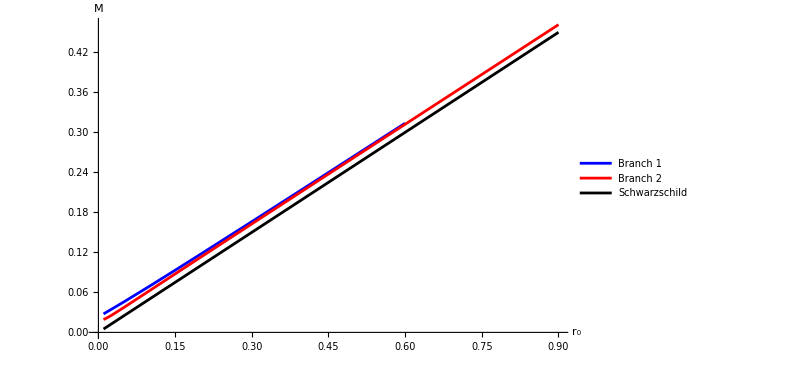

```mathematica
ListPlot[{Table[{X1[[i]][[1]],X1[[i]][[3]]},{i,1,10}],Table[{X2[[i]][[1]],X2[[i]][[3]]},{i,1,30}],Table[{X2[[i]][[1]],X2[[i]][[1]]/2},{i,1,30}]},PlotStyle->{Blue,Red,Black},Joined->{True,True,True},AxesLabel->{Style["r_0",FontSize->20],Style["M",FontSize->20]},PlotLegends->Placed[{Style["Branch 1",FontSize->18],Style["Branch 2",FontSize->18],Style["Schwarzschild",FontSize->18]},{0.2,0.9}],PlotRange->All,ImageSize->600]
```